## Initialize the notebook

```mathematica
ClearAll["Global`*"] (*Clears all variables*);
padding={{70, 10}, {50, 10}}; (*Space around plots*)
size=500;   (*Size of plots*)
SetOptions[Plot,BaseStyle->{FontFamily->"Optima",FontSize->10},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,ImagePadding->padding,ImageSize->size]; (*Sets Plots to have a certain look*)
SetOptions[ListPlot,BaseStyle->{FontFamily->"Optima",FontSize->10},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick},{Orange,Thick},{Magenta,Thick}},TicksStyle->Directive[Black,10],Frame->True,Joined->True,ImagePadding->padding,ImageSize->size];  (*Sets ListPlots to have a certain look*)
messageHandler=If[Last[#],Abort[]]&;
Internal`AddHandler["Message",messageHandler]; 
Off[General::munfl]
μs=10^-6;
kHz=10^3;
MHz=10^6; 
GHz=10^9;
```

## Create the Hamiltonian

```mathematica
(*stringToNumber interprets Lewis' string inputs as complex numbers*)
SetAttributes[stringToNumber,Listable];
stringToNumber[s_String]:=ToExpression[StringReplace[s,{"e"->" 10^","i"->" I"}]];
stringToNumber[s_]:=s;
```

```mathematica
(*Imports Lewis' file*)
import=Import["/Users/gabrielpatenotte/Downloads/20220624ramanCouplings_hf_up-sigp_dn-sigp.csv","Data"];
(*Finds the column names in Lewis' file*)
headers=import[[;;1]];
(*Finds the quantum numbers of each intermediate  state*)
qnumbers=import[[2;;,;;4]];
(*Finds all of the properties for each intermediate state. Applies stringToNumber*)
props=import[[2;;,5;;]];
props=stringToNumber[props];
(*We will compare every Rabi frequency to the 1165 intermediate state's Rabi frequencies*)
intqnumber=qnumbers[[3]];
intprops=props[[3]];
props[[All,1]]=props[[All,1]]-intprops[[1]];
props[[All,2;;3]]=props[[All,2;;3]]/intprops[[2]];
props[[All,4;;7]]=props[[All,4;;7]]/intprops[[7]];
(*Delete the extraneous columns that correspond to the Rabi magnitudes *)
props=props[[All,{1,3,4,5}]];
(*Select only the  states that have significant coupling. Significant coupling is defined as the ratio of the upleg Rabi frequency to the detuning*)
propsSig=Select[props,Abs[#[[2]]]>.2&] (*Modify the RHS of the inequality to select a different set of states to be in the Hamiltonian*)
HLength=Length[propsSig]+3
```

{{3.70584,-4.16342-0.890525 ⅈ,0.000245012-2.63529×10^-14 ⅈ,-0.00267246+4.43921×10^-15 ⅈ},{3.88645,0.657277+0.158181 ⅈ,0.00202365+2.41518×10^-15 ⅈ,-0.0444427-2.25022×10^-14 ⅈ},{0.,0.98567-0.168683 ⅈ,-0.0950388-1.41195×10^-13 ⅈ,1.+1.46318×10^-12 ⅈ},{3.69148,-0.890614-5.43586×10^-7 ⅈ,3.58898×10^-14-0.000247847 ⅈ,-3.58936×10^-15+0.0027039 ⅈ},{3.47269,0.244857+0.122085 ⅈ,0.0167401-2.77914×10^-16 ⅈ,-0.185203-1.30545×10^-15 ⅈ},{-0.805483,0.232576-0.0307873 ⅈ,0.345707-1.82369×10^-13 ⅈ,0.104553-5.59968×10^-14 ⅈ}}

9

```mathematica
Ham=ConstantArray[0,{HLength,HLength}];
Table[Ham[[i+1,i+1]]=propsSig[[i,1]] 2π GHz+Δu-ⅈ Γ/2,{i,1,Length[propsSig]}];
Ham[[1,1]]=0;Ham[[HLength-1,HLength-1]]=Δu-Δd+2π 0.475 MHz;Ham[[HLength,HLength]]=Δu-Δd;
Table[Ham[[1,i+1]]=Ωu/2 propsSig[[i,2]],{i,1,Length[propsSig]}];
Table[Ham[[i+1,1]]=(Ωu*)/2 propsSig[[i,2]]*,{i,1,Length[propsSig]}];
Table[Ham[[i+1,HLength-1;;]]=Ωd/2 propsSig[[i,3;;]],{i,1,Length[propsSig]}];
Table[Ham[[HLength-1;;,i+1]]=(Ωd*)/2 propsSig[[i,3;;]]*,{i,1,Length[propsSig]}];
MatrixForm[Ham]
H5=({{0, Ωu/2, α Ωu/2, 0, 0}, {Ωu/2, Δu-ⅈ Γ/2, 0, Ωd/2, β Ωd/2}, {α Ωu/2, 0, Δu+Δe-ⅈ Γ/2, 0, 0}, {0, Ωd/2, 0, Δu-Δd, 0}, {0, β Ωd/2, 0, 0, Δhf+Δu-Δd}});
```

(0 | (-2.08171-0.445263 ⅈ) Ωu | (0.328638+0.0790906 ⅈ) Ωu | (0.492835-0.0843414 ⅈ) Ωu | (-0.445307-2.71793×10^-7 ⅈ) Ωu | (0.122429+0.0610425 ⅈ) Ωu | (0.116288-0.0153937 ⅈ) Ωu | 0 | 0
(-2.08171+0.445263 ⅈ) Conjugate[Ωu] | 2.32845×10^10-(ⅈ Γ)/2+Δu | 0 | 0 | 0 | 0 | 0 | (0.000122506-1.31764×10^-14 ⅈ) Ωd | (-0.00133623+2.2196×10^-15 ⅈ) Ωd
(0.328638-0.0790906 ⅈ) Conjugate[Ωu] | 0 | 2.44193×10^10-(ⅈ Γ)/2+Δu | 0 | 0 | 0 | 0 | (0.00101182+1.20759×10^-15 ⅈ) Ωd | (-0.0222214-1.12511×10^-14 ⅈ) Ωd
(0.492835+0.0843414 ⅈ) Conjugate[Ωu] | 0 | 0 | 0.-(ⅈ Γ)/2+Δu | 0 | 0 | 0 | (-0.0475194-7.05973×10^-14 ⅈ) Ωd | (0.5+7.31591×10^-13 ⅈ) Ωd
(-0.445307+2.71793×10^-7 ⅈ) Conjugate[Ωu] | 0 | 0 | 0 | 2.31942×10^10-(ⅈ Γ)/2+Δu | 0 | 0 | (1.79449×10^-14-0.000123923 ⅈ) Ωd | (-1.79468×10^-15+0.00135195 ⅈ) Ωd
(0.122429-0.0610425 ⅈ) Conjugate[Ωu] | 0 | 0 | 0 | 0 | 2.18196×10^10-(ⅈ Γ)/2+Δu | 0 | (0.00837005-1.38957×10^-16 ⅈ) Ωd | (-0.0926016-6.52724×10^-16 ⅈ) Ωd
(0.116288+0.0153937 ⅈ) Conjugate[Ωu] | 0 | 0 | 0 | 0 | 0 | -5.061×10^9-(ⅈ Γ)/2+Δu | (0.172854-9.11847×10^-14 ⅈ) Ωd | (0.0522764-2.79984×10^-14 ⅈ) Ωd
0 | (0.000122506+1.31764×10^-14 ⅈ) Conjugate[Ωd] | (0.00101182-1.20759×10^-15 ⅈ) Conjugate[Ωd] | (-0.0475194+7.05973×10^-14 ⅈ) Conjugate[Ωd] | (1.79449×10^-14+0.000123923 ⅈ) Conjugate[Ωd] | (0.00837005+1.38957×10^-16 ⅈ) Conjugate[Ωd] | (0.172854+9.11847×10^-14 ⅈ) Conjugate[Ωd] | 2.98451×10^6-Δd+Δu | 0
0 | (-0.00133623-2.2196×10^-15 ⅈ) Conjugate[Ωd] | (-0.0222214+1.12511×10^-14 ⅈ) Conjugate[Ωd] | (0.5-7.31591×10^-13 ⅈ) Conjugate[Ωd] | (-1.79468×10^-15-0.00135195 ⅈ) Conjugate[Ωd] | (-0.0926016+6.52724×10^-16 ⅈ) Conjugate[Ωd] | (0.0522764+2.79984×10^-14 ⅈ) Conjugate[Ωd] | 0 | -Δd+Δu)

## Compute time evolution

```mathematica
shapeGaussian[x_,x0_,w_]=Exp[-(x-x0)^2/(2(w/(2 √(2Log[2])))^2)];
shapeGaussianSqrt[x_,x0_,w_]=Exp[-(x-x0)^2/(2(w/(2 √(2Log[2])))^2)]^(1/2);
pops[replacements_]:=Module[{tSim0,ψ,H,sols,init,cs,ps,ψ0,SE},
tSim0=tSim//.replacements;
H=Evaluate[Ham//.replacements];
ψ[t_]:=Table[ToExpression["c"<>ToString[i]][t],{i,1,HLength}];
cs:=Table[ToExpression["c"<>ToString[i]],{i,1,HLength}];
ps:=Table[ToExpression["p"<>ToString[i]],{i,1,HLength}];
ψ0=Flatten[{1,ConstantArray[0,HLength-1]}];
init=ψ[0]==ψ0;SE=ⅈ ψ'[t]==H.ψ[t];
sols=NDSolve[{SE,init},cs,{t,tSim0},PrecisionGoal->10,MaxSteps->1000000,Method->"StiffnessSwitching"];
ps=Abs[#[t μs]/.sols]^2&/@cs]
```

## Define supporting functions

```mathematica
(*Interpolation of the population evolution of each state over time*)
popInterps[rep_]:=pops[Normal[rep]][[{1,HLength-1,HLength}]]
(*Population of each state between the forward and reverse pulses*)
popM[rep_]:=Flatten[popInterps[rep]/.(t->tSim/(2μs)//.Normal[rep])]
(*Population of each state after the reverse pulse*)
popE[rep_]:=Flatten[popInterps[rep]/.(t->tSim/μs//.Normal[rep])]
(*Population of each state between the forward and reverse pulses, and after the reverse pulse.*)
popME[rep_]:=Module[{interps},interps=popInterps[rep];Flatten/@{interps/.(t->tSim/(2μs)//.rep),interps/.(t->tSim/μs//.Normal[rep])}]
(*Plot of the population of each state over time*)
plotStatePop[rep_]:=Module[{popOfTime,rep0},rep0=Normal[rep];popOfTime=popInterps[rep0];ListPlot[ParallelTable[{τ,#[[1]]/.t-> τ}&/@popOfTime,Evaluate[{τ,0,tSim/μs,1/400 tSim/μs}//.rep0]]ᵀ,PlotRange->{0,1},PlotLegends->LineLegend[{"p_Feshbach","p_(ground : FractionBox[1, 2], FractionBox[7, 2])","p_(ground : FractionBox[3, 2], FractionBox[5, 2])"},LabelStyle->Directive[FontSize->20,FontColor->Gray,FontFamily->"Optima"]],FrameLabel->{"Time (μs)","Population"}]]
(*Plot of the STIRAP pulses*)
plotStirapPulses[rep_]:=Plot[Evaluate[{Ωd/(2π MHz),Ωu/(2π MHz),Δd/(2π MHz),Δu/(2π MHz)}//.rep/.{t->t μs}],Evaluate[{t,0,tSim/μs}//.rep],PlotRange->All,PlotLegends->LineLegend[{"Ω_down","Ω_up","Δ_down","Δ_up"},LabelStyle->Directive[FontSize->20,FontColor->Gray,FontFamily->"Optima"]],FrameLabel->{"Time (μs)","Frequency (MHz)"}]
(*Plot of the population between the forward and reverse pulses as a function of scanned parameter*)
scan1Dm[rep_,mod_,unit_]:=Module[{repX,var,x,range,tab},repX=rep;range=Flatten[{x,mod[[2;;]]}];repX[mod[[1]]]=var;tab=ParallelTable[Thread[{x,popM[Normal[repX/.var->(x unit)]]}],range]ᵀ;ListPlot[tab,PlotRange->{0,1},PlotLegends->LineLegend[{"p_Feshbach","p_(ground : FractionBox[1, 2], FractionBox[7, 2])","p_(ground : FractionBox[3, 2], FractionBox[5, 2])"},LabelStyle->Directive[FontSize->20,FontColor->Gray,FontFamily->"Optima"]],FrameLabel->{StringForm["`` (``)",mod[[1]],unit],"Population"}]]
(*Plot of the population after the reverse pulse as a function of scanned parameter*)
scan1De[rep_,mod_,unit_]:=Module[{repX,var,x,range,tab},repX=rep;range=Flatten[{x,mod[[2;;]]}];repX[mod[[1]]]=var;tab=ParallelTable[Thread[{x,popE[Normal[repX/.var->(x unit)]]}],range]ᵀ;ListPlot[tab,PlotRange->{0,1},PlotLegends->LineLegend[{"p_Feshbach","p_(v = 22)","p_excited","p_ground","p_hf"},LabelStyle->Directive[FontSize->20,FontColor->Gray,FontFamily->"Optima"]],FrameLabel->{StringForm["`` (``)",mod[[1]],unit],"Population"}]]
```

## Outputs

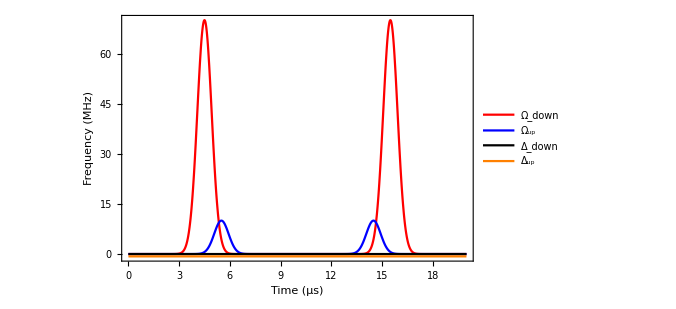

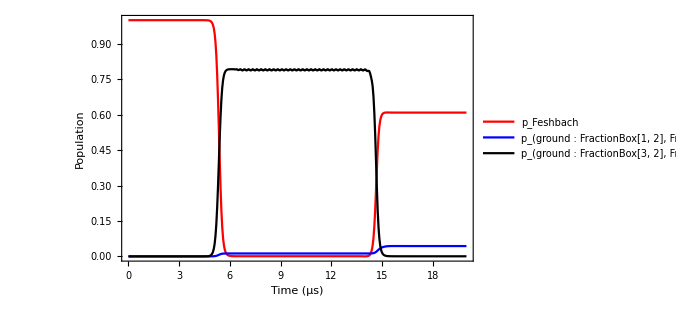

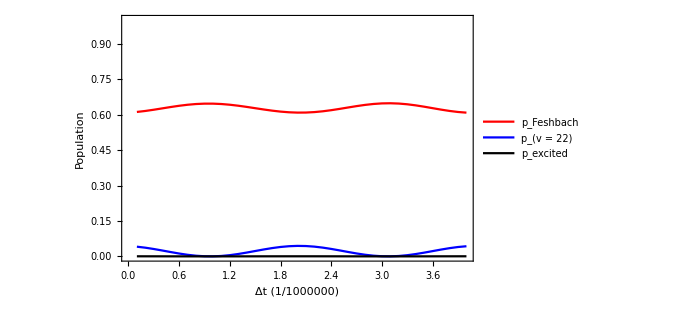

```mathematica
repS=<|Ωu-> Ω0u shapeGaussian[t,t2,w]+Ω0u shapeGaussian[t,tSim/2+t1+Δt,w],Ωd->Ω0d shapeGaussian[t,t1,w]+Ω0d shapeGaussian[t,tSim/2+t2+Δt,w],Δu->2π (-0.7) MHz,Δd->2π 0 MHz,Ω0u->2π 10 MHz,Ω0d->2π 70 MHz,t1->tSim/4-w/2,t2->tSim/4+w/2,Δt->0 μs,w->1 μs,Γ->2π 15 MHz,Δe->2π 3 GHz,α->9,tSim->20 w,β->0.1,Δhf-> 2π 0.476MHz|>;
(*repDR=<|Ωu->Ω0u,Ωd->Ω0d,Ω0u-> 2π 9 MHz,Ω0d->2π 40 MHz,Δu->δu+Δ,Δd->δd+Δ,Δ->2π 400 MHz,δu->2π (0) MHz,δd->2π (0) MHz,Γ->2π 15 MHz,tSim->w,w->10μs|>;*)(*
*)plotStirapPulses[repS]
plotStatePop[repS]
scan1De[repS,{Δt,.1,4,0.1},μs]
(*scan1Dm[repS,{Ω0d,3,50,2},2π MHz]*)
(*scan1Dm[repS,{Δu,-2,2,.1},2π MHz]*)
```

```mathematica
x={180,182,178,174,170,179,178,181,183,184,185,186,187,184,185};
y={2.4,3.4,2.5,1.7,3.3,4.2,4.3,2.9,1.3,0.6,1.3,1.4,1.8,1.8,1.5};
```

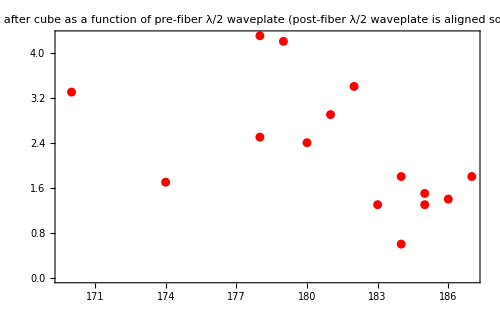

```mathematica
ListPlot[Transpose@{x,y},Joined->False,PlotLabel->"Power variation of F4 light after cube as a function of pre-fiber λ/2 waveplate\n(post-fiber λ/2 waveplate is aligned so that the cube output is 1/2P_(max))"]
```